```mathematica
(*~~ 1. Basic model trajectory ~~*)
DiffSystem1={
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
(*Trajectory plot*)
DiffNDSol = NDSolve[{DiffSystem1/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 0, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]->0, Subscript[γ, H]-> 0}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.DiffNDSol[[1,1]]], Evaluate[y[t]/.DiffNDSol[[1,2]]], Evaluate[w[t]/.DiffNDSol[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,0.72}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

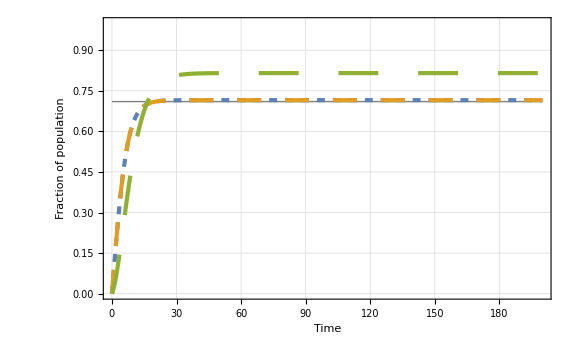

```mathematica
sol1 = NDSolve[{DiffSystem1/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
humantarget = Line[{{ 0, 0.71}, {200, 0.71}}];
Plot[{Evaluate[x[t]/.sol1[[1,1]]], Evaluate[y[t]/.sol1[[1,2]]], Evaluate[w[t]/.sol1[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,1.0}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, ImageSize->1024, FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large], Prolog->{Directive[{Thick, Gray}], humantarget}]
```

```mathematica
DiffSystem2={
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
```

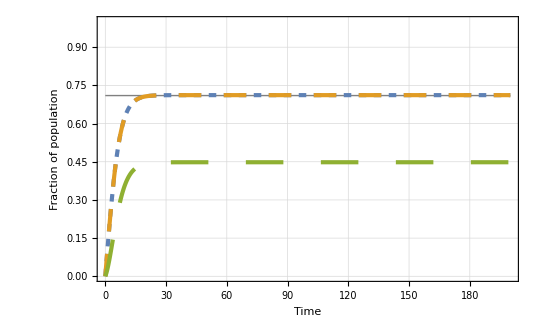

```mathematica
sol2 = NDSolve[{DiffSystem2/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol2[[1,1]]], Evaluate[y[t]/.sol2[[1,2]]], Evaluate[w[t]/.sol2[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,1.0}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, ImageSize->1024, FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],
Prolog->{Directive[{Thick, Gray}], humantarget}]
```

```mathematica
(*~~ 2. 3D plots {"β_AH","Λ_A", "R_H^*"} ~~*)
(*Plotting functions*)
EqSystem1 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
NSolSys1[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{EqSystem1[[1]]==0, EqSystem1[[2]]==0, EqSystem1[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals]
plot1env[bha_, bah_,LA_] := Evaluate[NSolSys1[1/10, LA, 1/10, 1/10, 1/10, 1/10, bah, 1/100, bha, 1/10, 1/10, 1/10, 1/10, 1/10, 1/5]][[1,1,2]]
plot1noenv[bha_, bah_,LA_] := Evaluate[NSolSys1[1/10, LA, 0, 0, 1/10, 1/10, bah, 0, bha, 0, 0, 0, 1/10, 1/10, 0]][[1,1,2]]
```

```mathematica
(*With environment, high impact*)
Plot3D[plot1env[1/10, par1, par2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}]
```

-Graphics3D-

```mathematica
(*No environment, high impact*)
Plot3D[plot1noenv[1/10, par1, par2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*~~ 2. Solve ~~*)
(* Step 1. Use equations for RE and RA, assuming steady RH *)
ODESystem3 = {
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x - Subscript[μ, e]*w[t]
};
```

```mathematica
(* Step 2. Solve this system for equilibrium *)
sol2 = DSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0}, {y,w},t, 
Assumptions->{Subscript[β, HA]≥ 0, Subscript[β, AA]≥ 0, Subscript[β, EA]≥ 0, Subscript[β, AE]≥ 0,Subscript[β, HE]≥ 0, Subscript[μ, e]≥ 0, Subscript[μ, A]≥ 0, x≥ 0, Subscript[γ, A]≥ 0, Subscript[γ, H]≥ 0, Subscript[Λ, A]≥ 0, Subscript[Λ, H]≥ 0}];
```

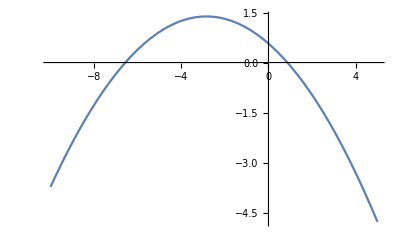

```mathematica
(*This gives us two solutions, with equations of quadratic form. We need to select the 'positive' solution.*)
(*Demonstrate for self satisfaction that we are working with quadratic functions *)
f[y_] := (1-y) * (0.1+0.1*0.7+0.1*y + 0.2 * 2)-0.1*y
Plot[f[w], {w, -10, 5}]
```

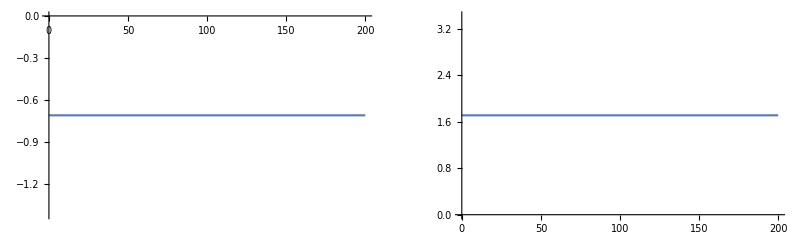

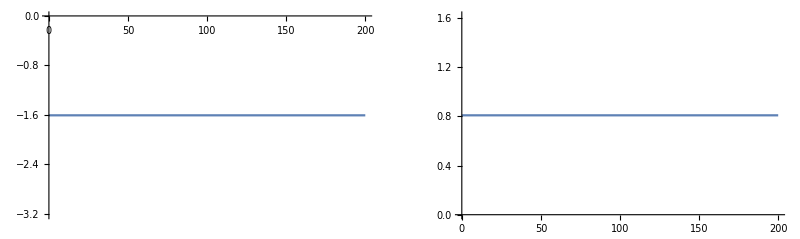

```mathematica
(* Step 3. Select correct solution. Have to plot the different solutions to look at what value they are suggesting*)
solv1 = sol2[[1]]; (*RA==0*)
solv2 = sol2[[2]]; (*RE==0*)
wv1 = Plot[Evaluate[w[t]/.solv1[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
wv2 = Plot[Evaluate[w[t]/.solv2[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{wv1, wv2}]
yv1 = Plot[Evaluate[y[t]/.solv1[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
yv2 = Plot[Evaluate[y[t]/.solv2[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{yv1, yv2}]
(*Solution two is the (biologically speaking) right solution. Now Try to simplify.*)
```

```mathematica
(*Simplify to get a simpler equation*)
yorigeq = solv2[[2, 2, 2]]; (*eq found above*)
yeq= FullSimplify[yorigeq]; (*can we get a simper one?*)
```

```mathematica
worigeq = solv2[[1, 2, 2]];
weq = FullSimplify[worigeq];
```

```mathematica
(*Looking at plots with RH on one axis and RA or RE on the other, and looking at conseqence of different parameter combinations.*)
(*Define functions so that we can make plots*)
yfunc[xs_, bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_ ] := yeq /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
wfunc[xs_,bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_]:= weq/.{Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1,Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
```

```mathematica
(*Can use a manipulate plot - but not on an i5*) (*Manipulate[Plot[{yfunc[par1, bea, bhe, bae, mue, Le], wfunc[par1, bea, bhe, bae, mue, Le]},{par1,0,1}, AxesLabel->{"R_H^*", "R^*"}, PlotRange->{{0,1},{0,3}}], {bea, 0, 1}, {bhe, 0, 1},{bae, 0, 1}, {mue, 0, 1.0}, {Le, 0, 0.1}]*)
```

```mathematica
(* Step 4. Solve analytical solutions for x*)
yeqx = Solve[yeq==y, x];(*x on right hand side*)
ytargfixedx= Solve[0.7 == yeqx[[1,1,2]], y]; (*for a given x, what par combinations/RA values are possible?*)
ytargfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1} (*find right solution*)
```

{{y→-2.21816},{y→0.723106}}⟦i,1,2⟧

```mathematica
yfixedxplot[La_, bHE_] :=Evaluate[ytargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[yfixedxplot[par1,par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

-Graphics3D-

```mathematica
weqx = Solve[{w == weq}, x];
weqx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1, w -> 2} (*which solution is positive?*)
```

{{x→16.7507},{x→-222.051}}⟦i,1,2⟧

```mathematica
wtargfixedx = Solve[0.7==weqx[[1,1,2]], w];
(*which solution is the right one*) 
wtargfixedx[[i,1,2]]/.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}
```

{{w→-1.03418},{w→0.954183}}⟦i,1,2⟧

```mathematica
wfixedxplot[La_, bHE_] :=Evaluate[wtargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[wfixedxplot[par1, par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

-Graphics3D-

```mathematica
(*~~ 3. Equilibrium analysis for sensitivity analysis ~~*)
parameters = Rest[Import["M:\\New projects\\Model env compartment\\paramodel.csv"]];
```

```mathematica
ODESystemFASTUnbounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
equilibriumUnbounded[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystemFASTUnbounded[[1]]==0, ODESystemFASTUnbounded[[2]]==0, ODESystemFASTUnbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
eqanalysisUnbounded = Table[equilibriumUnbounded[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibriumUnbounded.csv", eqanalysisUnbounded];
```

```mathematica
ODESystemFASTBounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
equilibriumBounded[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystemFASTBounded[[1]]==0, ODESystemFASTBounded[[2]]==0, ODESystemFASTBounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
eqanalysisBounded = Table[equilibriumBounded[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibriumBounded.csv", eqanalysisBounded];
```

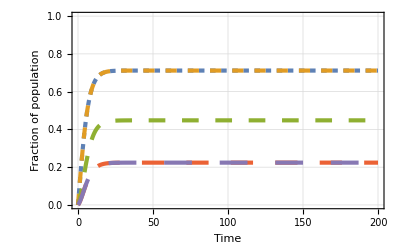

```mathematica
(*~~ 4. Fractions of RE contribution ~~*)
(*Trajectory plots*)
ODEboundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (1-w[t]) * (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
ODEunboundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
sol3 = NDSolve[{ODEboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol3[[1,1]]], Evaluate[y[t]/.sol3[[1,2]]], Evaluate[w[t]/.sol3[[1,3]]], Evaluate[z[t]/.sol3[[1,4]]], Evaluate[r[t]/.sol3[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

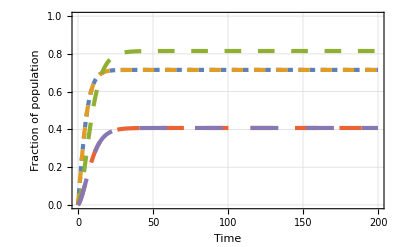

```mathematica
sol4 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
(*Look at impact of interventions on the environment*)
ODEunboundfracnondiff = {
(1 - x[t]) * (Subscript[Λ, H]+Subscript[β, AH]*y[t]+Subscript[β, HH]*x[t] + Subscript[β, EH]*w[t]) -Subscript[μ, H]*x[t],
(1 - y[t]) * (Subscript[Λ, A]+Subscript[β, HA]*x[t]+Subscript[β, AA]*y[t] + Subscript[β, EA]*w[t])-Subscript[μ, A]*y[t],
(Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
(Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
(Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
ODEboundfracnondiff = {
(1 - x[t]) * (Subscript[Λ, H]+Subscript[β, AH]*y[t]+Subscript[β, HH]*x[t] + Subscript[β, EH]*w[t]) -Subscript[μ, H]*x[t],
(1 - y[t]) * (Subscript[Λ, A]+Subscript[β, HA]*x[t]+Subscript[β, AA]*y[t] + Subscript[β, EA]*w[t])-Subscript[μ, A]*y[t],
(1-w[t])*(Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
(1-w[t])*(Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
(1-w[t])*(Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
```

```mathematica
(*functionc for plotting solutions*)
unboundsol1[bAE_, LA_, bEH_, bEA_] :=NSolve[{ODEunboundfracnondiff[[1]]==0, ODEunboundfracnondiff[[2]]==0, ODEunboundfracnondiff[[3]]==0, ODEunboundfracnondiff[[4]]==0, ODEunboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
boundsol1[bAE_, LA_, bEH_, bEA_] := NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
getFrac[n_, sol_] := sol[[1,n,2]] 
HAratio[sol_] := sol[[1,5,2]]/sol[[1,4,2]]
```

```mathematica
(*try looking at the impact - functions*)
RCHbf[bAE_, bEH_, bEA_]:= boundsol1[bAE,0, bEH, bEA][[1,1,2]]
RCHuf[bAE_, bEH_, bEA_] := unboundsol1[bAE,0, bEH, bEA][[1,1,2]]
RHbf[bAE_, LA_, bEH_, bEA_]:= boundsol1[bAE,LA, bEH, bEA][[1,1,2]]
RHuf[bAE_, LA_, bEH_, bEA_] := unboundsol1[bAE,LA, bEH, bEA][[1,1,2]]
impact[RH_, RCH_] := 1 - (RCH/RH)
```

```mathematica
(*plot impact*)
URHimpactmidEH = ContourPlot[impact[ RHuf[par1, par2, 1/100, 1/100], RCHuf[par1, 1/100, 1/100]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.14}}], PlotRange -> All];
BRHimpactmidEH = ContourPlot[impact[RHbf[par1, par2, 1/100, 1/100], RCHbf[par1, 1/100, 1/100]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.14}}], PlotRange -> All];
URHimpactnoEH = ContourPlot[impact[ RHuf[par1, par2, 0, 1/100], RCHuf[par1, 0, 1/100]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.14}}], PlotRange -> All];
BRHimpactnoEH = ContourPlot[impact[RHbf[par1, par2, 0, 1/100], RCHbf[par1, 0, 1/100]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.14}}], PlotRange -> All];
RHimpactnoEHnoEA = ContourPlot[impact[ RHuf[par1, par2, 0,0], RCHuf[par1, 0,0]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},   ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.14}}], PlotRange -> All];
```

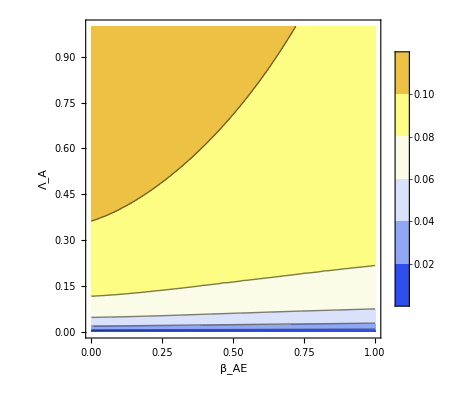
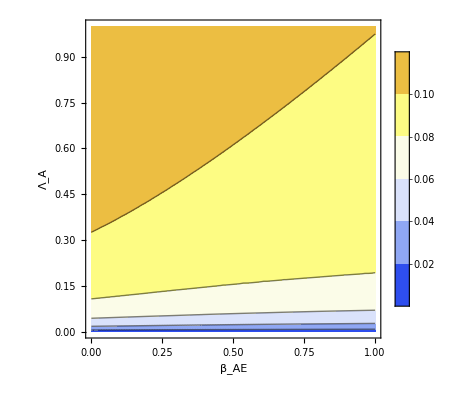
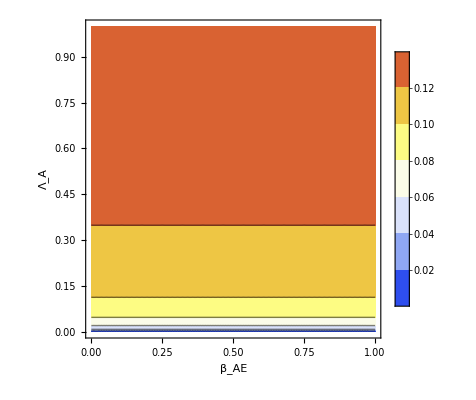
Row[-Graphics-,-Graphics-,-Graphics-]

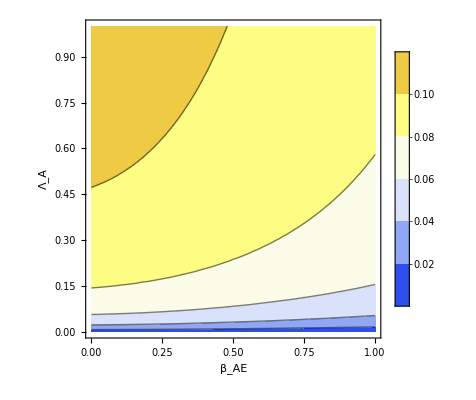
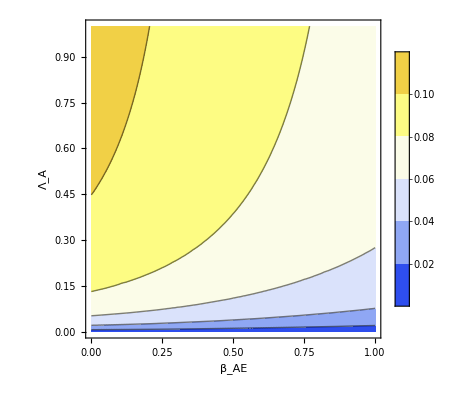
Row[-Graphics-,-Graphics-]

```mathematica
Row[BRHimpactmidEH,BRHimpactnoEH, RHimpactnoEHnoEA] 
Row[URHimpactmidEH, URHimpactnoEH]
```

```mathematica
(*~~ 5. How does curtailing ABx in animals affect and the controbution fo the environment to humans impact RH? ~~*)
```

```mathematica
(*Plot fraction of environment from animals*)
UmidEHlowHA = ContourPlot[unboundHAsol[par1, par2, 1/1000, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 6}}]];
BmidEHlowHA = ContourPlot[boundHAsol[par1, par2, 1/1000, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 1}}]];
UmidEHhighHA = ContourPlot[unboundHAsol[par1, par2, 1/10, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 6}}]];
BmidEHhighHA = ContourPlot[boundHAsol[par1, par2, 1/10, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 1}}]];
```

$Aborted

$Aborted

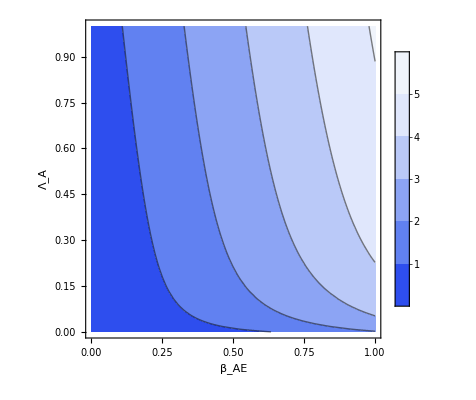
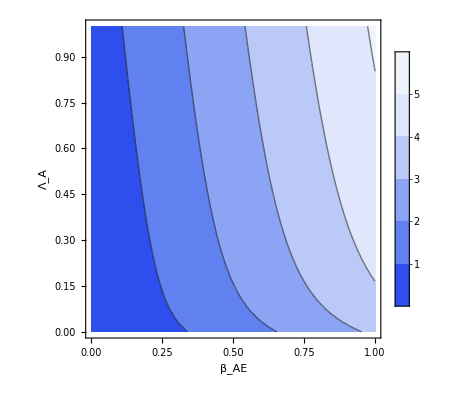
Row[-Graphics-,-Graphics-]

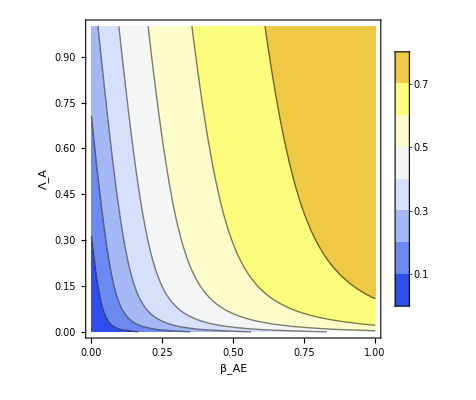
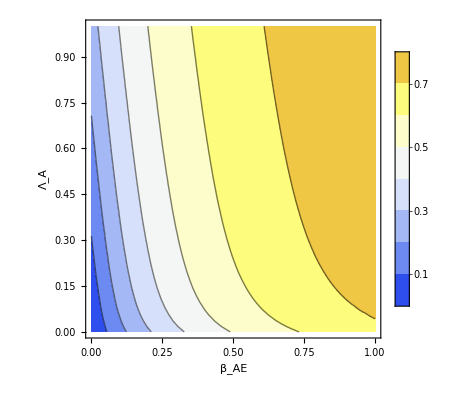
Row[-Graphics-,-Graphics-]

```mathematica
Row[UmidEHlowHA,UmidEHhighHA]
Row[BmidEHlowHA,BmidEHhighHA]
```

```mathematica
(* ---- 6. Changes to forces of infection ---- *)
(*Get force of infection from animals*)
FOIA[x_, y_, bAH_] :=bAH * y * (1-x)
(*Get force of infection from the environment*)
FOIE[x_, w_, bEH_] :=bEH * w * (1-x)
(*Get force of infection from other humans*)
FOIH[x_,  bHH_] :=bHH * x * (1-x)
(*Get force of infection from antibiotic usage*)
FOIab[x_, LH_] := LH * (1 - x)
```

```mathematica
(*Get RH for different environment structures based on bAH, bEH, bHH and LA*)
unboundsol[ LA_, bAH_, bEH_, bHH_] :=NSolve[{ODEunboundfracnondiff[[1]]==0, ODEunboundfracnondiff[[2]]==0, ODEunboundfracnondiff[[3]]==0, ODEunboundfracnondiff[[4]]==0, ODEunboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->bAH,Subscript[β, HH]-> bHH, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
boundsol[ LA_, bAH_, bEH_, bHH_] := NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->bAH,Subscript[β, HH]-> bHH, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
```

```mathematica
(*Get equilibrium values for different LA*)
xyw = Table[Table[boundsol[p1, 1/10, 1/10, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
xywU = Table[Table[unboundsol[p1, 1/10, 1/10, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
(*Get forces of infection*)
FOITab = Table[{FOIA[xyw[[row, 1]], xyw[[row, 2]], 1/10], FOIE[xyw[[row, 1]], xyw[[row, 3]],1/10], FOIH[xyw[[row,1]], 1/10], FOIab[xyw[[row, 1]], 1/10]}, {row, 4}] ;
FOITabU = Table[{FOIA[xywU[[row, 1]], xywU[[row, 2]], 1/10], FOIE[xywU[[row, 1]], xywU[[row, 3]],1/10], FOIH[xywU[[row,1]], 1/10], FOIab[xywU[[row, 1]], 1/10]}, {row, 4}] ;
(*Get proportions*)
sums = Table[Sum[FOITab[[n,i]],{i,4}], {n,4}];
props = Table[Table[FOITab[[n,i]]/sums[[n]], {i,4}], {n,4}];
sumsU = Table[Sum[FOITabU[[n,i]],{i,4}], {n,4}];
propsU = Table[Table[FOITabU[[n,i]]/sumsU[[n]], {i,4}], {n,4}];
```

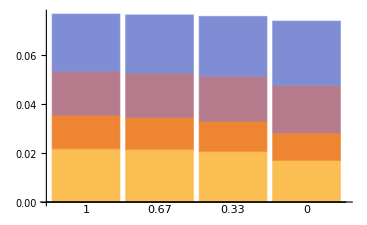
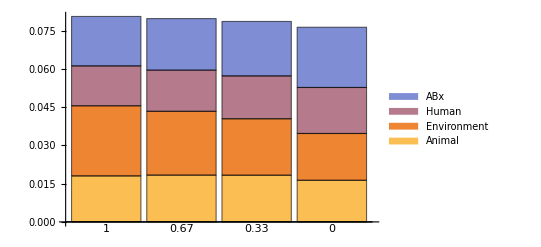
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[FOITab,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}],
BarChart[FOITabU,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

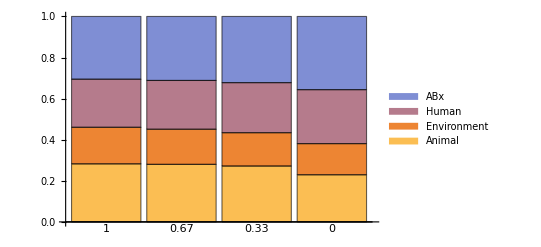
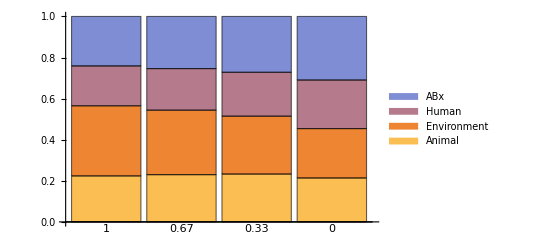
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[props,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}],
BarChart[propsU,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

```mathematica
(*Get forces of infection for animals*)
ABconsumption = {1.0, 0.67, 0.33, 0.0}
FOITabAnimal = Table[{FOIA[xyw[[row, 2]], xyw[[row, 2]], 1/10], FOIE[xyw[[row, 2]], xyw[[row, 3]],1/10], FOIA[xyw[[row,2]], xyw[[row, 1]], 1/10], FOIab[xyw[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
FOITabUAnimal = Table[{FOIA[xywU[[row, 2]], xywU[[row, 2]], 1/10], FOIE[xywU[[row, 2]], xywU[[row, 3]],1/10], FOIA[xywU[[row,2]], xywU[[row, 1]], 1/10], FOIab[xywU[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
(*Get proportions*)
sumsAnimal = Table[Sum[FOITabAnimal[[n,i]],{i,4}], {n,4}];
propsAnimal = Table[Table[FOITabAnimal[[n,i]]/sumsAnimal[[n]], {i,4}], {n,4}];
sumsUAnimal = Table[Sum[FOITabUAnimal[[n,i]],{i,4}], {n,4}];
propsUAnimal = Table[Table[FOITabUAnimal[[n,i]]/sumsUAnimal[[n]], {i,4}], {n,4}];
```

{1.,0.67,0.33,0.}

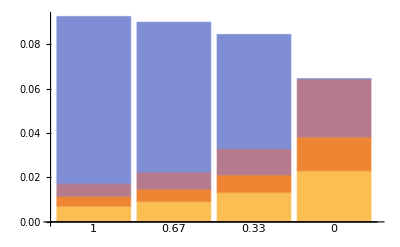
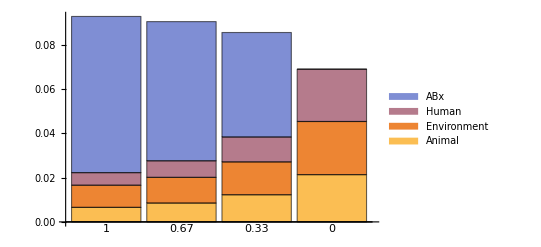
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[FOITabAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}],
BarChart[FOITabUAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

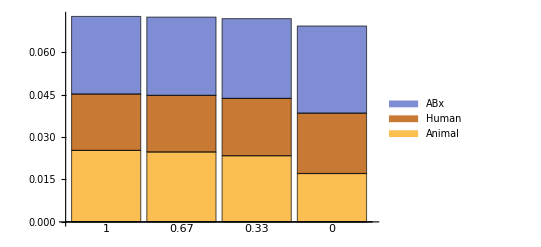
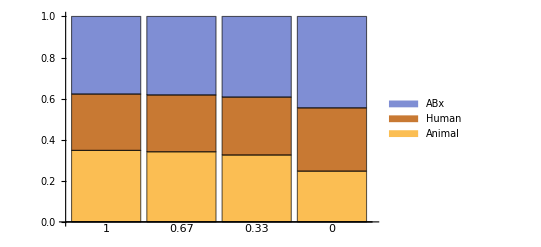
Row[-Graphics-,-Graphics-]

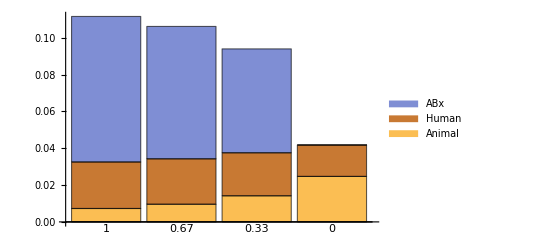
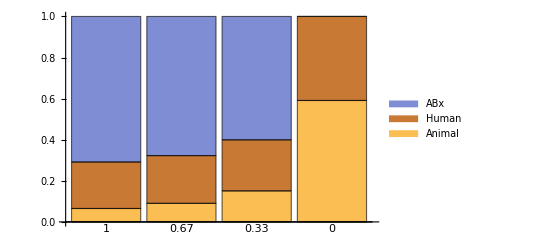
Row[-Graphics-,-Graphics-]

```mathematica
(*Compare to two compartment model*)
bound2compsol[ LA_, bAH_, bEH_, bHH_] := NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->bAH,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 0, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
(*Get equilibrium values for different LA*)
xyw2c = Table[Table[bound2compsol[p1, 1/10, 0, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
(*Get forces of infection*)
FOITab2comp = Table[{FOIA[xyw2c[[row, 1]], xyw2c[[row, 2]], 1/10], FOIH[xyw2c[[row,1]], 1/10], FOIab[xyw2c[[row, 1]], 1/10]}, {row, 4}] ;
(*Get proportions*)
sums2c = Table[Sum[FOITab2comp[[n,i]],{i,3}], {n,4}];
props2c = Table[Table[FOITab2comp[[n,i]]/sums2c[[n]], {i,3}], {n,4}];
(*Get forces of infection for animals*)
FOITab2compAnimal = Table[{FOIA[xyw2c[[row, 2]], xyw2c[[row, 2]], 1/10], FOIA[xyw2c[[row,1]],xyw2c[[row, 2]],  1/10], FOIab[xyw2c[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
(*Get proportions*)
sums2cAnimal = Table[Sum[FOITab2compAnimal[[n,i]],{i,3}], {n,4}];
props2cAnimal = Table[Table[FOITab2compAnimal[[n,i]]/sums2cAnimal[[n]], {i,3}], {n,4}];
Row[BarChart[FOITab2comp,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}],
BarChart[props2c,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}]]
Row[BarChart[FOITab2compAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}],
BarChart[props2cAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}]]
```

```mathematica
xyw2c
```

{{0.72578,0.920928,0.733099},{0.72346,0.892659,0.704677},{0.718076,0.828974,0.664097},{0.692021,0.554958,0.57392}}

```mathematica
(* ---- 7. Trajectory plots - what happens just after an intervention of animal ABx has been implemented? ---- *)
(*Get equilibrium values for Subscript[Λ, A]=0.1*) 
solest = NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RH = solest[[1,1,2]];
RA = solest[[1,2,2]];
RE = solest[[1,3,2]];
REh = solest[[1,4,2]];
REa = solest[[1,5,2]];
solest2 = NSolve[{ODEunboundfracnondiff[[1]]==0, ODEunboundfracnondiff[[2]]==0, ODEunboundfracnondiff[[3]]==0, ODEunboundfracnondiff[[4]]==0, ODEunboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RHu = solest2[[1,1,2]];
RAu = solest2[[1,2,2]];
REu = solest2[[1,3,2]];
REhu = solest2[[1,4,2]];
REau = solest2[[1,5,2]];
solest3 = NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1, Subscript[γ, A]->0, Subscript[γ, H]->0}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RH2 = solest3[[1,1,2]];
RA2 = solest3[[1,2,2]];
RE2 = solest3[[1,3,2]];
REh2 =0;
REa2 = 0;
```

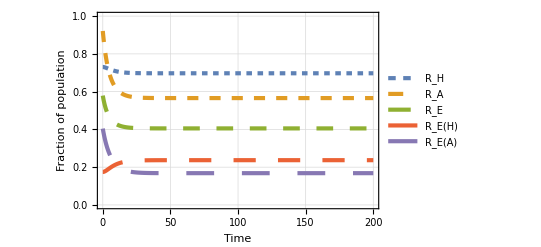

```mathematica
sol3 = NDSolve[{ODEboundfrac/.
{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == RH, y[0]== RA, w[0]==RE, z[0] == REh, r[0] == REa}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol3[[1,1]]], Evaluate[y[t]/.sol3[[1,2]]], Evaluate[w[t]/.sol3[[1,3]]], Evaluate[z[t]/.sol3[[1,4]]], Evaluate[r[t]/.sol3[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

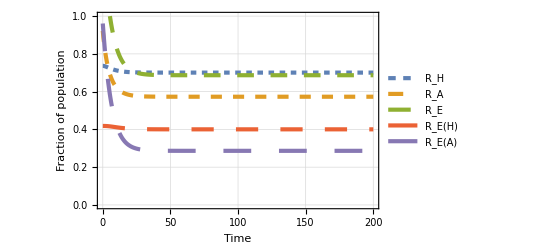

```mathematica
sol3 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == RHu, y[0]== RAu, w[0]==REu, z[0] == REhu, r[0] == REau}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol3[[1,1]]], Evaluate[y[t]/.sol3[[1,2]]], Evaluate[w[t]/.sol3[[1,3]]], Evaluate[z[t]/.sol3[[1,4]]], Evaluate[r[t]/.sol3[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"}, PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

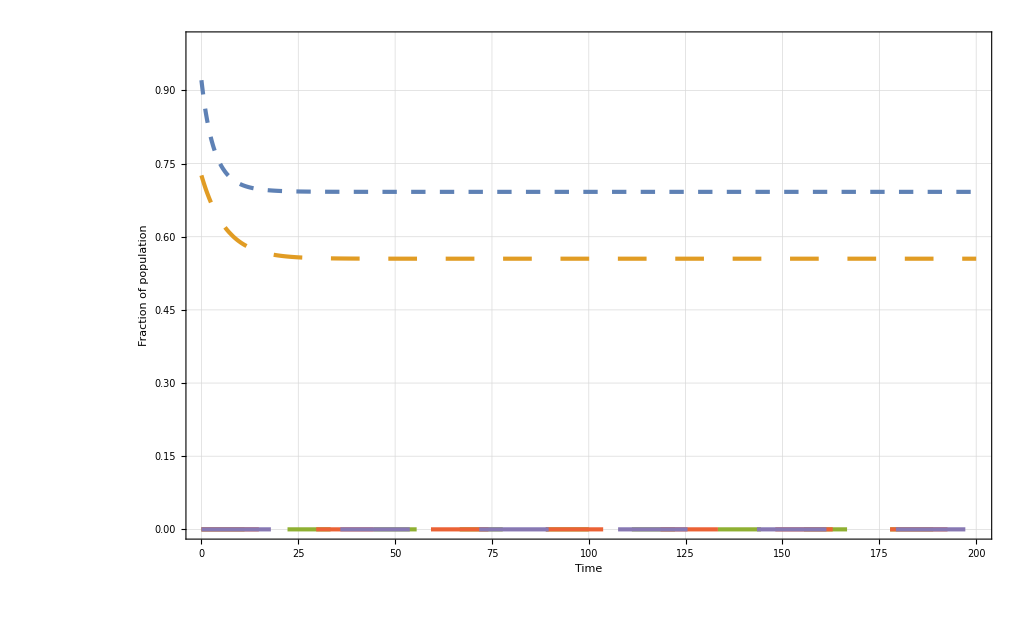

```mathematica
sol4 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 0, Subscript[γ, H]->0}, x[0] == RH2, y[0]== RA2, w[0]==RE2, z[0] == REh2, r[0] == REa2}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
RE2
```

0.261204